# L5PN Ca fit, PFC

#### Last update: HS April 2025: Status: Influx via different Cav driven by AP waveform with Unitstep function Buffering by cooperative CR and CR B5 with FF, ATP, EGTA or BAPTA, slow and fast endogenous buffers with estimted kinetics Concentrations in mol/m3 (i.e. factor 10^-3 gives mol/l)

## Edit

```mathematica
(*General settings*)
shells=200;                                (*1 based indexing; 1 is inner shell*)
TimeWindow=0.15;

young=0;
adult=1;
PFC=1;

(*APs and ISI*)
APN=1;
ISI=20.*10^-3;


DiscreteDist=0;
DistList={13};
(*DistList={2,3,4,5,6,7,8,9,10,11,12};*)
(*DistList={2,3,4,5,6,7,8};*)
CaRest =  29.*10^-6; (*10^-9/10^-3, i.e. in nM*)
FF=0.2;                (*IF of CR in innermost shell*)

(*Chelator settings*)
native=0;                                  (*native = 1 removes Ca indicator dye*)
low=1;                                       (*1 = Fluo5F, 0 = OGB1*)

LF=0.7;
cFluo=200.*10^-3*LF;             (*70% of Pipette concentration; 10^-6/10^-3, i.e. in µM; 2.*10^-3 as endogenous buffer; cf L5PN Ca fit*)
cOGB=75.*10^-3*LF;

(*Plotting & Calculating*)
FusPlot=0;
CaPlot=1;
AvCaPlot=1;
CalPr=0;



(*Buffer capacity; used to calculate concentrations of unknown edogenous buffers*)

κS=25.;        (*120.*)      (*for EB + 3 for ATP = 123; 105-135; Helmchen et al., Biophys J, 1996; no substantial mobility, no wash-out;  140 for L2/3 in Koester & Sakmann, J Physiol, 2000; kappa fix =100 in CA1, Matthews et al., J Neurosci, 2013 but not in Pyramids*)

kOffFBscale=1; (*0.1, 1, 10*)
FSB=0.07;     (*fraction of slow EB; 0, 0.07, 0.1*)
FFB=1-FSB;     (*fraction of fast EB*)
FFSB=0.5;  (*fixed fraction of SB*)
FFFB=0.5;    (*fixed fraction of FB*)


(*AP and Cav and Pump*)


(*young, different kappaS*)
If[young==1,
If[κS==120,
NPQ=12;
NN=7;  
NR=1;
NL=0;];

If[κS==25,
NPQ=7;
NN=5;  
NR=0.5;
NL=0;];

If[κS==7,
NPQ=6;
NN=4;  
NR=0.65;
NL=0;];
];

If[adult==1,
NPQ=33;
NN=0;
NR=0;
NL=0;]

ECa=130*10^-3;
Vrest=-80*10^-3;
(*γ=4.*10^-4;*)                (*pumprate 1/s; gamma is the free parameter*)
γ=3.2*10^-4;
```

## Geometry & Constants

```mathematica
(*Vb=0.127*10^-18 m^3; Schikorski & Stevens, PNAS, 1999; olfactory cortex; corrected for space occupied by vesicles and organelles, factor 0.635 (Wilhelm et al., Science, 2014): 0.2 * 0.635*)

DCa =220 *10^-12;    (*DiffCo; m2/s*)
NA = 6.022*10^23;  (*Teilchen/mol; Avogadros Number*)
F=96485.;    (*C/mol; Farraday*)

ClearAll[Vs,As]

r=0.4*10^-6;    

ds = r/shells;
Vs[0]=0;
As[0]=0;
For[i=1,i≤shells,i++,     Vs[i]=2/3*π*(i*ds)^3-2/3*π*((i-1)*ds)^3     (*;Print[Vs[i]]  *) ](*hemi-spheres; in m3*)
For[i=1,i≤shells,i++,     As[i]=2*π*(i*ds)^2 ]
(*hemi-spheres; in m^2*)


VsTotal =2/3*π*(shells*ds)^3;
(*Print["Test V =  ",VsTotal,  " =  ",∑_(s=1)^shells (Vs[s])]
Print["spatial resolution = ", ds, "m"]*)
```

## Influx

### Action potential and Ca channels

#### APs: Unitstep with Double Exp Function

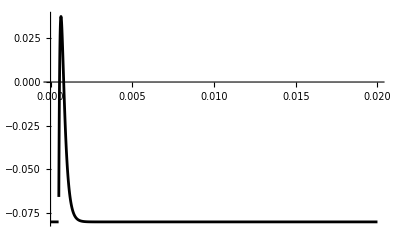

```mathematica
Clear[Vm,startT,taud,taur]
startT=0.5*10^-3;
taud=0.2*10^-3;              (*Borst et al., JP, 1995*)
taur=0.1*10^-3;

Vm=Sum[(UnitStep[t-i]*(Exp[-(t-i)/taud]-Exp[-(t-i)/taur])),{i,startT,startT+(APN-1)*ISI,ISI}];
Vm=0.47*Vm-0.08;
plAP=Plot[Vm,{t,0,APN*ISI},PlotRange->All,PlotStyle->Black]
```

#### P/Q type channel

(Li et al., J Neurosci, 2007; cf. Ermolyuk et al., Nat Neurosci, 2013 and Scimemi et al., J Neurosci, 2012)

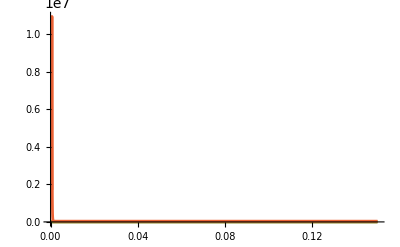

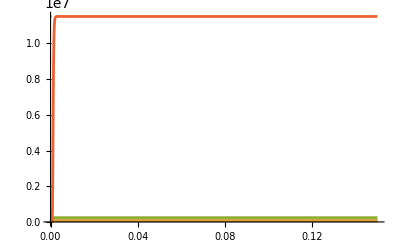

```mathematica
Clear[α,Α,β,Β]

gPQ=2.5*10^-12;   (*pS; assumed values as in the above papers*)

α[1]=5.89*10^3;
α[2]=9.21*10^3;
α[3]=5.2*10^3;
α[4]=1823.18*10^3;
Α=247.71*10^3;

β[1]=14.99*10^3;
β[2]=6.63*10^3;
β[3]=132.8*10^3;
β[4]=248.58*10^3;
Β=8.28*10^3;

k[1]=62.61*10^-3;
k[2]=33.92*10^-3;
k[3]=135.08*10^-3;
k[4]=20.86*10^-3;

Table[alpha[i]=α[i] Exp[Vm/k[i]],{i,1,4}];
Table[beta[i]=β[i] Exp[-Vm/k[i]],{i,1,4}];

Plot[{alpha[1],alpha[2],alpha[3],alpha[4]},{t,0,TimeWindow},PlotRange->All]
Plot[{beta[1],beta[2],beta[3],beta[4]},{t,0,TimeWindow},PlotRange->All]
```

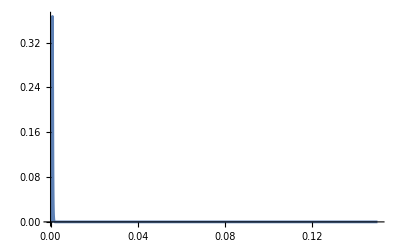

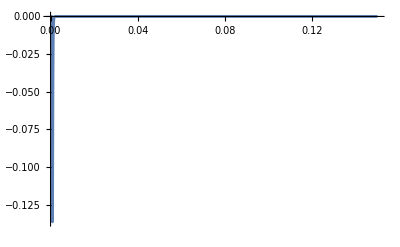

```mathematica
PQChannel={
PQCh0[0]==1,
PQCh1[0]==0,
PQCh2[0]==0,
PQCh3[0]==0,
PQCh4[0]==0,
PQChOpen[0]==0,

PQCh0'[t]==-PQCh0[t]*alpha[1]+PQCh1[t]*beta[1],

PQCh1'[t]==-PQCh0'[t]-PQCh1[t]*alpha[2]+PQCh2[t]*beta[2],

PQCh2'[t]==PQCh1[t]*alpha[2]-PQCh2[t]*beta[2]-PQCh2[t]*alpha[3]+PQCh3[t]*beta[3],

PQCh3'[t]==PQCh2[t]*alpha[3]-PQCh3[t]*beta[3]-PQCh3[t]*alpha[4]+PQCh4[t]*beta[4],

PQCh4'[t]==PQCh3[t]*alpha[4]-PQCh4[t]*beta[4]-PQCh4[t]*Α+PQChOpen[t]*Β,

PQChOpen'[t]==PQCh4[t]*Α-PQChOpen[t]*Β};



VarsPQ={PQCh0,PQCh1,PQCh2,PQCh3,PQCh4,PQChOpen};

solPQ:=NDSolve[PQChannel,VarsPQ,{t,0,TimeWindow},MaxStepSize->0.001]

Plot[Evaluate[{PQChOpen[t]}/.solPQ],{t,0,TimeWindow},PlotRange->All]

Plot[Evaluate[10^12*gPQ*(Vm-ECa)*{PQChOpen[t]}/.solPQ],{t,0,TimeWindow},PlotRange->{0,-0.15}]
```

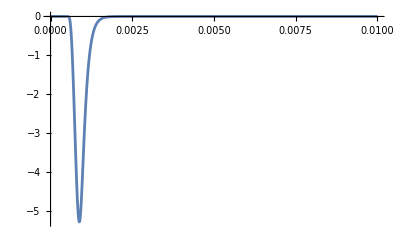

{{0.00187454}}

{{151.313}}

```mathematica
InfluxPQ:=(1/(2   F*Vs[1]))*gPQ*(Vm-ECa)*PQChOpen[t]

(*InfluxPQ:=Evaluate[(1/(2*F* Vs[1]))*gPQ*(Vm-ECa)*{PQChOpen[t]}/.solPQ]*)
(*Plot[InfluxPQ,{t,0,0.01},PlotRange->All]*)

InPQ:=Evaluate[(1/(2*F* VsTotal))*gPQ*(Vm-ECa)*{PQChOpen[t]}/.solPQ]
Plot[InPQ,{t,0,0.01},PlotRange->All]
conc=NIntegrate[-InPQ,{t,0,TimeWindow}]
CaIons=conc*NA*VsTotal
```

#### N type channel

(Li et al., J Neurosci, 2007; cf. Ermolyuk et al., Nat Neurosci, 2013 and Scimemi et al., J Neurosci, 2012)

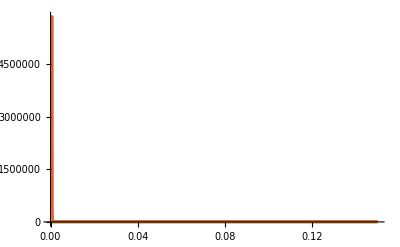

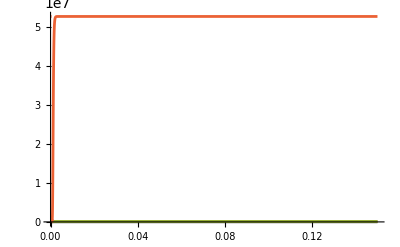

```mathematica
Clear[αN,ΑN,βN,ΒN]

gN=2.5*10^-12;

αN[1]=4.29*10^3;
αN[2]=5.24*10^3;
αN[3]=4.98*10^3;
αN[4]=772.63*10^3;
ΑN=615.01*10^3;

βN[1]=5.23*10^3;
βN[2]=6.63*10^3;
βN[3]=73.89*10^3;
βN[4]=692.18*10^3;
ΒN=7.68*10^3;

kN[1]=68.75*10^-3;
kN[2]=39.53*10^-3;
kN[3]=281.62*10^-3;
kN[4]=18.46*10^-3;

Table[alphaN[i]=αN[i] Exp[Vm/kN[i]],{i,1,4}];
Table[betaN[i]=βN[i] Exp[-Vm/kN[i]],{i,1,4}];

Plot[{alphaN[1],alphaN[2],alphaN[3],alphaN[4]},{t,0,TimeWindow},PlotRange->All]
Plot[{betaN[1],betaN[2],betaN[3],betaN[4]},{t,0,TimeWindow},PlotRange->All]
```

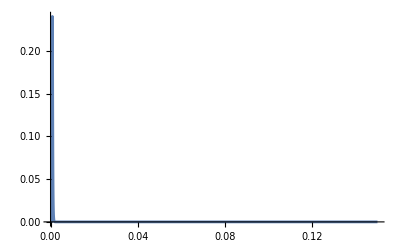

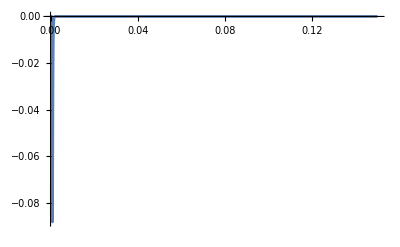

```mathematica
NChannel={
NCh0[0]==1,
NCh1[0]==0,
NCh2[0]==0,
NCh3[0]==0,
NCh4[0]==0,
NChOpen[0]==0,

NCh0'[t]==-NCh0[t]*alphaN[1]+NCh1[t]*betaN[1],

NCh1'[t]==-NCh0'[t]-NCh1[t]*alphaN[2]+NCh2[t]*betaN[2],

NCh2'[t]==NCh1[t]*alphaN[2]-NCh2[t]*betaN[2]-NCh2[t]*alphaN[3]+NCh3[t]*betaN[3],

NCh3'[t]==NCh2[t]*alphaN[3]-NCh3[t]*betaN[3]-NCh3[t]*alphaN[4]+NCh4[t]*betaN[4],

NCh4'[t]==NCh3[t]*alphaN[4]-NCh4[t]*betaN[4]-NCh4[t]*ΑN+NChOpen[t]*ΒN,

NChOpen'[t]==NCh4[t]*ΑN-NChOpen[t]*ΒN};



VarsN:={NCh0,NCh1,NCh2,NCh3,NCh4,NChOpen}

solN:=NDSolve[NChannel,VarsN,{t,0,TimeWindow},MaxStepSize->0.001]

Plot[Evaluate[{NChOpen[t]}/.solN],{t,0,TimeWindow},PlotRange->All]

Plot[Evaluate[10^12*gN*(Vm-ECa)*{NChOpen[t]}/.solN],{t,0,TimeWindow},PlotRange->{0,-0.15}]
```

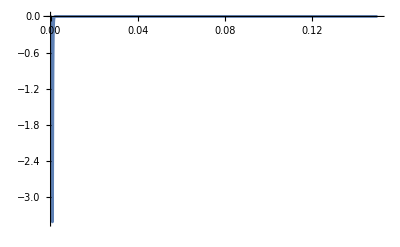

{{0.00118089}}

{{95.3211}}

```mathematica
InfluxN:=(1/(2 F  Vs[1]))*gN*(Vm-ECa)*NChOpen[t]

InN:=Evaluate[(1/(2 F  VsTotal))*gN*(Vm-ECa)*{NChOpen[t]}/.solN]
Plot[InN,{t,0,TimeWindow},PlotRange->All]
concN=NIntegrate[-InN,{t,0,TimeWindow}]
CaIonsN=concN*NA*VsTotal
```

#### R type channel

(Li et al., J Neurosci, 2007; cf. Ermolyuk et al., Nat Neurosci, 2013 and Scimemi et al., J Neurosci, 2012)

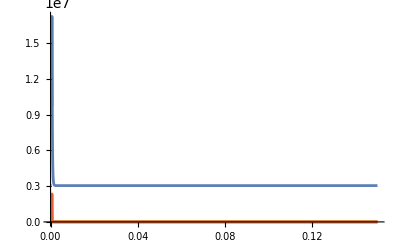

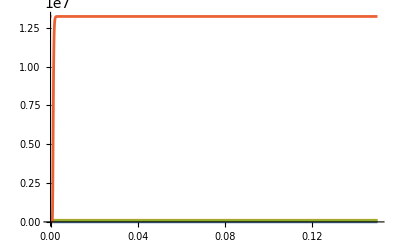

```mathematica
Clear[αR,ΑR,βR,ΒR]

gR=2.5*10^-12;

αR[1]=9911.36*10^3;
αR[2]=4.88*10^3;
αR[3]=4*10^3;
αR[4]=256.41*10^3;
ΑR=228.83*10^3;

βR[1]=0.62*10^3;
βR[2]=21.91*10^3;
βR[3]=51.3*10^3;
βR[4]=116.97*10^3;
ΒR=1.78*10^3;

kR[1]=67.75*10^-3;
kR[2]=50.94*10^-3;
kR[3]=173.29*10^-3;
kR[4]=16.92*10^-3;

Table[alphaR[i]=αR[i] Exp[Vm/kR[i]],{i,1,4}];
Table[betaR[i]=βR[i] Exp[-Vm/kR[i]],{i,1,4}];

Plot[{alphaR[1],alphaR[2],alphaR[3],alphaR[4]},{t,0,TimeWindow},PlotRange->All]
Plot[{betaR[1],betaR[2],betaR[3],betaR[4]},{t,0,TimeWindow},PlotRange->All]
```

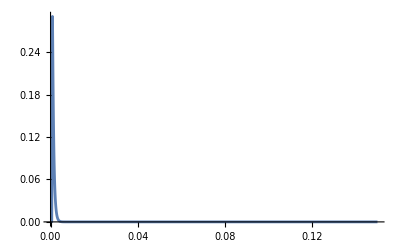

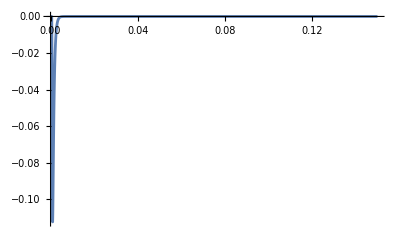

```mathematica
RChannel={
RCh0[0]==1,
RCh1[0]==0,
RCh2[0]==0,
RCh3[0]==0,
RCh4[0]==0,
RChOpen[0]==0,

RCh0'[t]==-RCh0[t]*alphaR[1]+RCh1[t]*betaR[1],

RCh1'[t]==-RCh0'[t]-RCh1[t]*alphaR[2]+RCh2[t]*betaR[2],

RCh2'[t]==RCh1[t]*alphaR[2]-RCh2[t]*betaR[2]-RCh2[t]*alphaR[3]+RCh3[t]*betaR[3],

RCh3'[t]==RCh2[t]*alphaR[3]-RCh3[t]*betaR[3]-RCh3[t]*alphaR[4]+RCh4[t]*betaR[4],

RCh4'[t]==RCh3[t]*alphaR[4]-RCh4[t]*betaR[4]-RCh4[t]*ΑR+RChOpen[t]*ΒR,

RChOpen'[t]==RCh4[t]*ΑR-RChOpen[t]*ΒR};



VarsR:={RCh0,RCh1,RCh2,RCh3,RCh4,RChOpen}

solR:=NDSolve[RChannel,VarsR,{t,0,TimeWindow},MaxStepSize->0.001]

Plot[Evaluate[{RChOpen[t]}/.solR],{t,0,TimeWindow},PlotRange->All]

Plot[Evaluate[10^12*gR(Vm-ECa)*{RChOpen[t]}/.solR],{t,0,TimeWindow},PlotRange->{0,-0.15}]
```

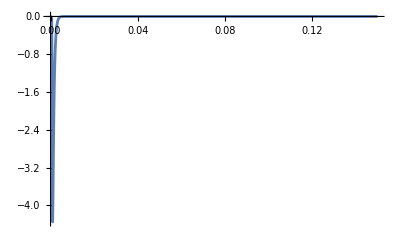

{{0.00407883}}

{{329.242}}

```mathematica
InfluxR:=(1/(2 F  Vs[1]))*gR*(Vm-ECa)*RChOpen[t]

InR:=Evaluate[(1/(2 F  VsTotal))*gR*(Vm-ECa)*{RChOpen[t]}/.solR]
Plot[InR,{t,0,TimeWindow},PlotRange->All]
concR=NIntegrate[-InR,{t,0,TimeWindow}]
CaIonsR=concR*NA*VsTotal
```

#### L type channel simple

(Beyl et al., J Gen Physiol, 2009)

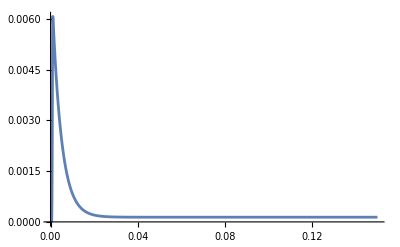

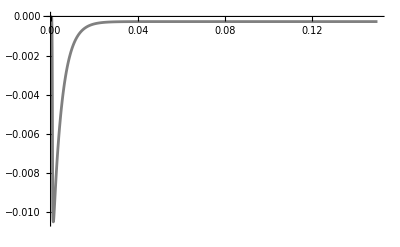

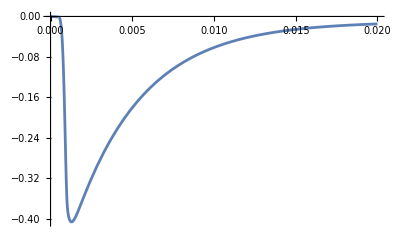

{{0.00206967}}

{{167.063}}

```mathematica
Clear[αL,ΑL,βL,ΒL]

gL=9.*10^-12;   (*von Wegner & Fink, Eur Biophys J, 2010.*)

αL=0.427*10^3;
ΑL=0.15*10^3;

βL=0.216*10^3;
ΒL=0.24*10^3;

kLa=328.8*10^-3;
kLb=9.04*10^-3;

alphaL=αL Exp[Vm/kLa];
betaL=βL Exp[-Vm/kLb];

LChannel={
LCh0[0]==1,
LCh1[0]==0,
LChOpen[0]==0,

LCh0'[t]==-LCh0[t]*alphaL+LCh1[t]*betaL,

LCh1'[t]==-LCh0'[t]-LCh1[t]*ΑL+LChOpen[t]*ΒL,

LChOpen'[t]==LCh1[t]*ΑL-LChOpen[t]*ΒL};


VarsL:={LCh0,LCh1,LChOpen}

solL:=NDSolve[LChannel,VarsL,{t,0,TimeWindow},MaxStepSize->0.001]

Plot[Evaluate[{LChOpen[t]}/.solL],{t,0,TimeWindow},PlotRange->All]

plL=Plot[Evaluate[10^12*gL(Vm-ECa)*{LChOpen[t]}/.solL],{t,0,TimeWindow},PlotRange->{0,-0.15},PlotStyle->Gray]
InfluxL:=(1/(2 F Vs[1]))*gL*(Vm-ECa)*LChOpen[t]
InL:=Evaluate[(1/(2 F VsTotal))*gL*(Vm-ECa)*{LChOpen[t]}/.solL]
Plot[InL,{t,0,0.02},PlotRange->All]
concL=NIntegrate[-InL,{t,0,0.02}]
CaIonsL=concL*NA*VsTotal
```

#### Or: L type channel simple 2

(von Wegner & Fink, Eur Biophys J, 2010)

```mathematica
(*Clear[VarsL,LChannel,solL]
gL=24*10^-12;
V0=0.035;

f=0.85*10.^3;
g=2*10.^3;
α0L=2*10.^3;
α1L=0.012*10.^3;
β0L=0.0882*10.^3;
β1L=-0.05*10^3;

αL=α0L*Exp[α1L*(Vm-V0)];
βL=β0L*Exp[β1L*(Vm-V0)];

Plot[{αL},{t,0,0.004},PlotRange->All]
Plot[{βL},{t,0,0.004},PlotRange->All]

LChannel={
C0[0]==1,
C1[0]==0,
C2[0]==0,
C3[0]==0,
C4[0]==0,
LO[0]==0,

C0'[t]==-4* αL* C0[t]+βL *C1[t],
C1'[t]==4* αL *C0[t]-βL* C1[t]-3* αL* C1[t]+2* βL* C2[t],
C2'[t]==3* αL *C1[t]-2* βL *C2[t]-2 *αL* C2[t]+3* βL* C3[t],
C3'[t]==2 *αL* C2[t]-3* βL* C3[t]-αL* C3[t]+4 *βL* C4[t],
C4'[t]== αL* C3[t]-4* βL *C4[t]-f* C4[t]+g* LO[t],
LO'[t]== f* C4[t]-g* LO[t]
};


VarsL={C0,C1,C2,C3,C4,LO};


solL:=NDSolve[LChannel,VarsL,{t,0,TimeWindow}]

IL=10^12*gL*LO[t]*(Vm-ECa);
InfluxL:=(1/(2 F Vs[1]))*gL*(Vm-ECa)*LO[t]
InL:=Evaluate[(1/(2 F VsTotal))*gL*(Vm-ECa)*{LO[t]}/.solL]
Plot[InL,{t,0,0.004},PlotRange->All]
concL=NIntegrate[-InL,{t,0,0.004}]
CaIonsL=concL*NA*VsTotal

plL2=Plot[Evaluate[IL/.solL],{t,0,0.004},PlotRange->All]*)
```

## Buffering

### OGB1 or Fluo5F

Fluo - 5 F 
(kon / koff:  3*10^8 / 300 (Scott & Rusakov, J Neurosci, 2006); 2.4*10^8 / 543 (from Schmidt et al. Curr Biol, 2013))
(Kd 585 (Brenowitz & Regehr, J Neurosci, 2007); 1.3 or 0.76 (our calibrations)) 
OGB1 kinetics
Schmidt et al. JP 2003

```mathematica
OGtotal =If[native==1,0,If[low==1, cFluo,cOGB]] ;

kOnOG  = If[low==1, 6.834*10^5,4.3*10^5];     
kOffOG = If[low==1,300.,140.];             

(*kOnOG  = If[low==1, 3.*10^5,4.3*10^5];     (*This gives the same; so it does not matter if you adjust kon or koff *)
kOffOG = If[low==1,135.,140.];   *)
  
KdOG =kOffOG/kOnOG
DOG = 220.*10^-12;


kappaOG=OGtotal/KdOG;

RestOG=OGtotal/(CaRest/KdOG+1.);
RestCaOG= OGtotal - RestOG;



BufferOG=Join[
(* t=0 equations *)
Table[OG[i][0]==RestOG,{i,1,shells}],
Table[{CaOG[i][0]==RestCaOG},{i,1,shells}],

(* f' equations for shell1 *)
{OG[1]'[t]==-kOnOG*Ca[1][t]* OG[1][t]+ kOffOG *CaOG[1][t]
+ DOG *As[1]/(Vs[1]*ds)*(OG[2][t]-OG[1][t])},

{CaOG[1]'[t]==kOnOG*Ca[1][t]* OG[1][t]- kOffOG *CaOG[1][t]- DOG *As[1]/(Vs[1]*ds)*(CaOG[1][t]-CaOG[2][t])},

(* f' equations for 2 to shells-1 *)
Table[
{OG[i]'[t]==-kOnOG*Ca[i][t]* OG[i][t]- DOG *As[i-1]/(Vs[i]*ds)*(OG[i][t]-OG[i-1][t])+ kOffOG *CaOG[i][t]
+ DOG *As[i]/(Vs[i]*ds)*(OG[i+1][t]-OG[i][t])},{i,2,shells-1}],
Table[
{CaOG[i]'[t]==kOnOG*Ca[i][t]* OG[i][t]+ DOG *As[i-1]/(Vs[i]*ds)*(CaOG[i-1][t]-CaOG[i][t])- kOffOG *CaOG[i][t]- DOG *As[i]/(Vs[i]*ds)*(CaOG[i][t]-CaOG[i+1][t])},{i,2,shells-1}],

(* f' equations for outermost shell *)

{OG[shells]'[t]==-kOnOG*Ca[shells][t]* OG[shells][t]+ kOffOG *CaOG[shells][t]
- DOG *As[shells-1]/(Vs[shells]*ds)*(OG[shells][t]-OG[shells-1][t])},

{CaOG[shells]'[t]==kOnOG*Ca[shells][t]* OG[shells][t]- kOffOG *CaOG[shells][t]+ DOG*As[shells-1]/(Vs[shells]*ds)*(CaOG[shells-1][t]-CaOG[shells][t])}

];

BufferOG = Flatten[BufferOG];

Print["KD in µM: ", KdOG*10^3]
```

0.000438982

KD in µM: 0.438982

### ATP

```mathematica
ATPtotal = 600.*10^-3 ;(*total free pipette concentration*)(*90% of free pipette concentration of 600 µM =540 µM Kd Mg = 100 µM => only ~ 64 ATP free;      anything between 64 and 600 goes!*)    
DATP = 220.*10^-12;                                        (*Meinrencken et al., 2002;*)
kOnATP  = 5*10^5;
kOffATP = 100000.;
KdATP = kOffATP/kOnATP;
kappaATP=ATPtotal/KdATP

RestATP=ATPtotal/(CaRest/KdATP+1.);
RestCaATP= ATPtotal - RestATP;
```

3.

#### Buffer equations ATP

```mathematica
BufferATP=Join[
(* t=0 equations *)
Table[ATP[i][0]==RestATP,{i,1,shells}],
Table[CaATP[i][0]==RestCaATP,{i,1,shells}],

(* f' equations for shell1 *)
{ATP[1]'[t]==-kOnATP*Ca[1][t]* ATP[1][t]+ kOffATP *CaATP[1][t]
+ DATP *As[1]/(Vs[1]*ds)*(ATP[2][t]-ATP[1][t])},

{CaATP[1]'[t]==kOnATP*Ca[1][t]* ATP[1][t]- kOffATP *CaATP[1][t]- DATP *As[1]/(Vs[1]*ds)*(CaATP[1][t]-CaATP[2][t])},

(* f' equations for 2 to shells-1 *)
Table[
{ATP[i]'[t]==-kOnATP*Ca[i][t]* ATP[i][t]- DATP *As[i-1]/(Vs[i]*ds)*(ATP[i][t]-ATP[i-1][t])+ kOffATP *CaATP[i][t]
+ DATP *As[i]/(Vs[i]*ds)*(ATP[i+1][t]-ATP[i][t])},{i,2,shells-1}],
Table[
{CaATP[i]'[t]==kOnATP*Ca[i][t]* ATP[i][t]+ DATP *As[i-1]/(Vs[i]*ds)*(CaATP[i-1][t]-CaATP[i][t])- kOffATP *CaATP[i][t]- DATP *As[i]/(Vs[i]*ds)*(CaATP[i][t]-CaATP[i+1][t])},{i,2,shells-1}],

(* f' equations for outermost shell *)

{ATP[shells]'[t]==-kOnATP*Ca[shells][t]* ATP[shells][t]+ kOffATP *CaATP[shells][t]
- DATP *As[shells-1]/(Vs[shells]*ds)*(ATP[shells][t]-ATP[shells-1][t])},

{CaATP[shells]'[t]==kOnATP*Ca[shells][t]* ATP[shells][t]- kOffATP *CaATP[shells][t]+ DATP*As[shells-1]/(Vs[shells]*ds)*(CaATP[shells-1][t]-CaATP[shells][t])}

];


BufferATP = Flatten[BufferATP];
```

### CR

```mathematica
CRtotal =0.*10^-3;
                                
CRBVtotal =0.*10^-3;
              

DCR = 20*10^-12 ;

kOnT=1.8*10^3;
kOffT=53.;   
KdT = kOffT/kOnT;

kOnR=3.1*10^5;
kOffR=20.;   
KdR = kOffR/kOnR;

kOnCRapp = √(kOnT*kOnR)        ;
kOffCRapp = √(kOffT*kOffR)        ;
KdCRapp = kOffCRapp /kOnCRapp ;

(*independent BS V*)
kOnBV=5.*10^5;
kOffBV=5000.;   
KdCRBV = kOffBV/kOnBV;

kappCR=0.5 CRtotal/KdCRapp;
kappaR=CRtotal/KdR;
kappaT=CRtotal/KdT;
kappaBV=CRBVtotal/KdCRBV
```

0.

#### Resting conditions for CR

```mathematica
RestCRBV=CRBVtotal/(CaRest/KdCRBV+1.);
RestCaCRBV= CRBVtotal - RestCRBV;

RuheCR=Join[
(* t=0 equations *)
{RestCR[0]==CRtotal},
{RestCaCR[0]==0},
{RestCa2CR[0]==0},

(* f' equations *)
{RestCR'[x]==-(RestCaCR'[x]+RestCa2CR'[x])},
{RestCaCR'[x]==2*kOnT*CaRest* RestCR[x] - kOffT *RestCaCR[x]-kOnR*CaRest* RestCaCR[x] + 2*kOffR *RestCa2CR[x]},
{RestCa2CR'[x]==kOnR*CaRest* RestCaCR[x] - 2*kOffR *RestCa2CR[x]}

];

solCR := NDSolve[RuheCR,{RestCR,RestCaCR,RestCa2CR},{x,0.,1.}]; 

(*Plot[Evaluate[{10^6*RestCaCR[x]/.solCR,10^6*RestCa2CR[x]/.solCR,10^6*RestCR[x]/.solCR},{x,0.,1.}],PlotRange->All,AxesLabel->µM,PlotLabel->"Synapse, CaCR"]*)

IniCR = Extract[RestCR[1.]/.solCR,1];
IniCaCR = Extract[RestCaCR[1.]/.solCR,1];
IniCa2CR = Extract[RestCa2CR[1.]/.solCR,1];
```

#### Buffer equations CR

```mathematica
BufferCR=Join[
(* t=0 equations *)
Table[{CR[i][0]==IniCR},{i,1,shells}],
Table[{CaCR[i][0]==IniCaCR},{i,1,shells}],
Table[{Ca2CR[i][0]==IniCa2CR},{i,1,shells}],

(* f' equations for shell1 *)
{CR[1]'[t]==-2*kOnT*Ca[1][t]* CR[1][t] + kOffT *CaCR[1][t]
+(1-FF) DCR *As[1]/(Vs[1]*ds)*(CR[2][t]-CR[1][t])},
{CaCR[1]'[t]==2*kOnT*Ca[1][t]* CR[1][t] - kOffT *CaCR[1][t]
-kOnR*Ca[1][t]* CaCR[1][t] + 2*kOffR *Ca2CR[1][t]
-(1-FF) DCR *As[1]/(Vs[1]*ds)*(CaCR[1][t]-CaCR[2][t])},
{Ca2CR[1]'[t]==kOnR*Ca[1][t]* CaCR[1][t] - 2*kOffR *Ca2CR[1][t]
-(1-FF) DCR *As[1]/(Vs[1]*ds)*(Ca2CR[1][t]-Ca2CR[2][t])},


(* f' equations for 2 to shells-1 *)
Table[
{CR[i]'[t]==-2*kOnT*Ca[i][t]* CR[i][t] + kOffT *CaCR[i][t]
+(1-FF) DCR *As[i]/(Vs[i]*ds)*(CR[i+1][t]-CR[i][t])
-(1-FF)DCR *As[i-1]/(Vs[i]*ds)*(CR[i][t]-CR[i-1][t])},{i,2,shells-1}],
Table[
{CaCR[i]'[t]==2*kOnT*Ca[i][t]* CR[i][t] - kOffT *CaCR[i][t]
-kOnR*Ca[i][t]* CaCR[i][t] + 2*kOffR *Ca2CR[i][t]
+(1-FF)DCR *As[i-1]/(Vs[i]*ds)*(CaCR[i-1][t]-CaCR[i][t])
-(1-FF)DCR *As[i]/(Vs[i]*ds)*(CaCR[i][t]-CaCR[i+1][t])},{i,2,shells-1}],
Table[
{Ca2CR[i]'[t]==kOnR*Ca[i][t]* CaCR[i][t] - 2*kOffR *Ca2CR[i][t]
+(1-FF)DCR *As[i-1]/(Vs[i]*ds)*(Ca2CR[i-1][t]-Ca2CR[i][t])
-(1-FF)DCR *As[i]/(Vs[i]*ds)*(Ca2CR[i][t]-Ca2CR[i+1][t])},
{i,2,shells-1}],


(* f' equations for outermost shell *)
{CR[shells]'[t]==-2*kOnT*Ca[shells][t]* CR[shells][t] +kOffT *CaCR[shells][t]
-(1-FF)DCR *As[shells-1]/(Vs[shells]*ds)*(CR[shells][t]-CR[shells-1][t])},
{CaCR[shells]'[t]==2*kOnT*Ca[shells][t]* CR[shells][t] - kOffT *CaCR[shells][t]
-kOnR*Ca[shells][t]* CaCR[shells][t] +2*kOffR *Ca2CR[shells][t]
+(1-FF)DCR *As[shells-1]/(Vs[shells]*ds)*(CaCR[shells-1][t]-CaCR[shells][t])},
{Ca2CR[shells]'[t]==kOnR*Ca[shells][t]* CaCR[shells][t] - 2*kOffR *Ca2CR[shells][t]
+(1-FF)DCR *As[shells-1]/(Vs[shells]*ds)*(Ca2CR[shells-1][t]-Ca2CR[shells][t])}
];
BufferCR = Flatten[BufferCR];

BufferBV=Join[
(* t=0 equations *)
Table[CRBV[i][0]==RestCRBV,{i,1,shells}],
Table[CaCRBV[i][0]==RestCaCRBV,{i,1,shells}],

(* f' equations for shell1 *)
{CRBV[1]'[t]==-kOnBV*Ca[1][t]* CRBV[1][t]+ kOffBV *CaCRBV[1][t]
+ (1-FF)*DCR *As[1]/(Vs[1]*ds)*(CRBV[2][t]-CRBV[1][t])},

{CaCRBV[1]'[t]==kOnBV*Ca[1][t]* CRBV[1][t]- kOffBV *CaCRBV[1][t]- DCR *As[1]/(Vs[1]*ds)*(CaCRBV[1][t]-CaCRBV[2][t])},

(* f' equations for 2 to shells-1 *)
Table[
{CRBV[i]'[t]==-kOnBV*Ca[i][t]* CRBV[i][t]-(1-FF)* DCR *As[i-1]/(Vs[i]*ds)*(CRBV[i][t]-CRBV[i-1][t])+ kOffBV *CaCRBV[i][t]
+ (1-FF)*DCR *As[i]/(Vs[i]*ds)*(CRBV[i+1][t]-CRBV[i][t])},{i,2,shells-1}],
Table[
{CaCRBV[i]'[t]==kOnBV*Ca[i][t]* CRBV[i][t]+(1-FF)* DCR *As[i-1]/(Vs[i]*ds)*(CaCRBV[i-1][t]-CaCRBV[i][t])- kOffBV *CaCRBV[i][t]-(1-FF)* DCR *As[i]/(Vs[i]*ds)*(CaCRBV[i][t]-CaCRBV[i+1][t])},{i,2,shells-1}],

(* f' equations for outermost shell *)

{CRBV[shells]'[t]==-kOnBV*Ca[shells][t]* CRBV[shells][t]+ kOffBV *CaCRBV[shells][t]
-(1-FF)* DCR *As[shells-1]/(Vs[shells]*ds)*(CRBV[shells][t]-CRBV[shells-1][t])},

{CaCRBV[shells]'[t]==kOnBV*Ca[shells][t]* CRBV[shells][t]- kOffBV *CaCRBV[shells][t]+ (1-FF)*DCR*As[shells-1]/(Vs[shells]*ds)*(CaCRBV[shells-1][t]-CaCRBV[shells][t])}

];

BufferBV = Flatten[BufferBV];
```

### Unknown slow endogenous buffer

L5PNs do not express large amounts of EB with known kinetics (Celio, Neurosci, 1990; Baimbridge et al., TINS, 1992); therefore, unknonwn EB is assumed; Assumptions: EGTA-like slow binding kinetics (biphasic Ca Signal, Lee et al., J Physiol, 2000, Schmidt et al., J Physiol, 2003);

```mathematica
DSB=0.*10^-12; (*buffers have no substantial mobility in L5PNs; Helmchen et al., Biophys J, 1996*)
                                        
kOnSB  = 1.*10^4;(*Naraghi, 1997:2.6*10^6, 0.468; Nägerl et al., 2000: 1*10^7; 0.7; Kd 70 nM*)
kOffSB = 0.7;
KdSB = kOffSB/kOnSB;

SBtotal = κS*FSB*KdSB; (*Calculated from kappaS*)
kappaSB=SBtotal/KdSB;

RestSB=SBtotal/(CaRest/KdSB+1.);
RestCaSB= SBtotal - RestSB;

Print["KdSB (nM) ", 10^6*KdSB]
Print["conc. SB (µM) ", SBtotal*1000]
Print["kappa SB ", kappaSB]
```

KdSB (nM) 70.

conc. SB (µM) 0.1225

kappa SB 1.75

#### Buffer equations SB

```mathematica
BufferSB=Join[
(* t=0 equations *)
Table[SB[i][0]==(1-FFSB)*RestSB,{i,1,shells}],
Table[{CaSB[i][0]==(1-FFSB)*RestCaSB},{i,1,shells}],

(* f' equations for shell1 *)
{SB[1]'[t]==-kOnSB*Ca[1][t]* SB[1][t]+ kOffSB *CaSB[1][t]
+ DSB *As[1]/(Vs[1]*ds)*(SB[2][t]-SB[1][t])},

{CaSB[1]'[t]==kOnSB*Ca[1][t]* SB[1][t]- kOffSB *CaSB[1][t]- DSB *As[1]/(Vs[1]*ds)*(CaSB[1][t]-CaSB[2][t])},

(* f' equations for 2 to shells-1 *)
Table[
{SB[i]'[t]==-kOnSB*Ca[i][t]* SB[i][t]- DSB *As[i-1]/(Vs[i]*ds)*(SB[i][t]-SB[i-1][t])+ kOffSB *CaSB[i][t]
+ DSB *As[i]/(Vs[i]*ds)*(SB[i+1][t]-SB[i][t])},{i,2,shells-1}],
Table[
{CaSB[i]'[t]==kOnSB*Ca[i][t]* SB[i][t]+ DSB *As[i-1]/(Vs[i]*ds)*(CaSB[i-1][t]-CaSB[i][t])- kOffSB *CaSB[i][t]- DSB *As[i]/(Vs[i]*ds)*(CaSB[i][t]-CaSB[i+1][t])},{i,2,shells-1}],

(* f' equations for outermost shell *)

{SB[shells]'[t]==-kOnSB*Ca[shells][t]* SB[shells][t]+ kOffSB *CaSB[shells][t]
- DSB *As[shells-1]/(Vs[shells]*ds)*(SB[shells][t]-SB[shells-1][t])},

{CaSB[shells]'[t]==kOnSB*Ca[shells][t]* SB[shells][t]- kOffSB *CaSB[shells][t]+ DSB*As[shells-1]/(Vs[shells]*ds)*(CaSB[shells-1][t]-CaSB[shells][t])}

];

BufferSB = Flatten[BufferSB];

BufferSBf=Join[
(* t=0 equations *)
Table[SBf[i][0]==(FFSB)*RestSB,{i,1,shells}],
Table[{CaSBf[i][0]==(FFSB)*RestCaSB},{i,1,shells}],

(* f' equations for shell1 *)
{SBf[1]'[t]==-kOnSB*Ca[1][t]* SBf[1][t]+ kOffSB *CaSBf[1][t]},

{CaSBf[1]'[t]==kOnSB*Ca[1][t]* SBf[1][t]- kOffSB *CaSBf[1][t]},

(* f' equations for 2 to shells-1 *)
Table[
{SBf[i]'[t]==-kOnSB*Ca[i][t]* SBf[i][t]+ kOffSB *CaSBf[i][t]},{i,2,shells-1}],

Table[
{CaSBf[i]'[t]==kOnSB*Ca[i][t]* SBf[i][t]- kOffSB *CaSBf[i][t]},{i,2,shells-1}],

(* f' equations for outermost shell *)

{SBf[shells]'[t]==-kOnSB*Ca[shells][t]* SBf[shells][t]+ kOffSB *CaSBf[shells][t]},

{CaSBf[shells]'[t]==kOnSB*Ca[shells][t]* SBf[shells][t]- kOffSB *CaSBf[shells][t]}

];

BufferSBf = Flatten[BufferSBf];
```

### Unknown fast endogenous buffer

Assumption according to Vyleta&Jonas, Science, 2014; Klingauf & Neher, Biophys J, 1997 (comparable to CaM; Faas et al., 2004)

```mathematica
DFB=0.*10^-12; (*buffers have no substantial mobility in L5PNs; Helmchen et al., Biophys J, 1996*)
                                        
kOnFB  = 5.*10^5;    (*Vyleta & Jonas, 2014*)
kOffFB = kOffFBscale *1000.;
KdFB = kOffFB/kOnFB;


FBtotal = κS*FFB*KdFB ;(*Calculated from kappaS*)

kappaFB=FBtotal/KdFB;

RestFB=FBtotal/(CaRest/KdFB+1.);
RestCaFB= FBtotal - RestFB;

Print["KdFB (µM) ", 10^3*KdFB]
Print["conc. FB (µM) ", FBtotal*1000]
Print["kappa FB ", kappaFB]
```

KdFB (µM) 2.

conc. FB (µM) 46.5

kappa FB 23.25

#### Buffer equations FB

```mathematica
BufferFB=Join[
(* t=0 equations *)
Table[FB[i][0]==(1-FFFB)*RestFB,{i,1,shells}],
Table[{CaFB[i][0]==(1-FFFB)*RestCaFB},{i,1,shells}],

(* f' equations for shell1 *)
{FB[1]'[t]==-kOnFB*Ca[1][t]* FB[1][t]+ kOffFB *CaFB[1][t]
+ DFB *As[1]/(Vs[1]*ds)*(FB[2][t]-FB[1][t])},

{CaFB[1]'[t]==kOnFB*Ca[1][t]* FB[1][t]- kOffFB *CaFB[1][t]- DFB *As[1]/(Vs[1]*ds)*(CaFB[1][t]-CaFB[2][t])},

(* f' equations for 2 to shells-1 *)
Table[
{FB[i]'[t]==-kOnFB*Ca[i][t]* FB[i][t]- DFB *As[i-1]/(Vs[i]*ds)*(FB[i][t]-FB[i-1][t])+ kOffFB *CaFB[i][t]
+ DFB *As[i]/(Vs[i]*ds)*(FB[i+1][t]-FB[i][t])},{i,2,shells-1}],
Table[
{CaFB[i]'[t]==kOnFB*Ca[i][t]* FB[i][t]+ DFB *As[i-1]/(Vs[i]*ds)*(CaFB[i-1][t]-CaFB[i][t])- kOffFB *CaFB[i][t]- DFB *As[i]/(Vs[i]*ds)*(CaFB[i][t]-CaFB[i+1][t])},{i,2,shells-1}],

(* f' equations for outermost shell *)

{FB[shells]'[t]==-kOnFB*Ca[shells][t]* FB[shells][t]+ kOffFB *CaFB[shells][t]
- DFB *As[shells-1]/(Vs[shells]*ds)*(FB[shells][t]-FB[shells-1][t])},

{CaFB[shells]'[t]==kOnFB*Ca[shells][t]* FB[shells][t]- kOffFB *CaFB[shells][t]+ DFB*As[shells-1]/(Vs[shells]*ds)*(CaFB[shells-1][t]-CaFB[shells][t])}

];

BufferFB = Flatten[BufferFB];

BufferFBf=Join[
(* t=0 equations *)
Table[FBf[i][0]==(FFFB)*RestFB,{i,1,shells}],
Table[{CaFBf[i][0]==(FFFB)*RestCaFB},{i,1,shells}],

(* f' equations for shell1 *)
{FBf[1]'[t]==-kOnFB*Ca[1][t]* FBf[1][t]+ kOffFB *CaFBf[1][t]},

{CaFBf[1]'[t]==kOnFB*Ca[1][t]* FBf[1][t]- kOffFB *CaFBf[1][t]},

(* f' equations for 2 to shells-1 *)
Table[
{FBf[i]'[t]==-kOnFB*Ca[i][t]* FBf[i][t]+ kOffFB *CaFBf[i][t]},{i,2,shells-1}],

Table[
{CaFBf[i]'[t]==kOnFB*Ca[i][t]* FBf[i][t]- kOffFB *CaFBf[i][t]},{i,2,shells-1}],

(* f' equations for outermost shell *)

{FBf[shells]'[t]==-kOnFB*Ca[shells][t]* FBf[shells][t]+ kOffFB *CaFBf[shells][t]},

{CaFBf[shells]'[t]==kOnFB*Ca[shells][t]* FBf[shells][t]- kOffFB *CaFBf[shells][t]}

];

BufferFBf = Flatten[BufferFBf];
```

### Buffer Vars and Eqns

```mathematica
(*VarsBuffer:={CR,CaCR,Ca2CR,CRBV,CaCRBV,OG, CaOG,ATP,CaATP,EB,CaEB,MB,CaMB}*)

VarsBuffer:=Table[{OG[i], CaOG[i],ATP[i],CaATP[i],CR[i],CaCR[i],Ca2CR[i],CRBV[i],CaCRBV[i],SB[i], CaSB[i],SBf[i], CaSBf[i],FB[i], CaFB[i],FBf[i], CaFBf[i]},{i,1,shells}]

VarsBuffer=Flatten[VarsBuffer];

EqnsBuffer:=Flatten[Join[{BufferOG},{BufferATP},{BufferCR},{BufferBV},{BufferSB},{BufferSBf},{BufferFB},{BufferFBf}]]
```

## Calcium

```mathematica
ClearAll[Vars,Eqns]

FreeCa:= Join[
(* t=0 equations*)
Table[Ca[i][0]==CaRest,{i,1,shells}],

(*equations for shell1*)
{Ca[1]'[t]== 

NPQ*(-InfluxPQ)+NN*(-InfluxN)+NR*(-InfluxR)+NL*(-InfluxL)
(*InfluxS*)
-DCa*As[1]/(Vs[1]*ds)(Ca[1][t]-Ca[2][t])
- kOnATP*Ca[1][t]* ATP[1][t]+ kOffATP *CaATP[1][t]
-2*kOnT*Ca[1][t]* CR[1][t] + kOffT *CaCR[1][t]
-kOnR*Ca[1][t]* CaCR[1][t] + 2*kOffR *Ca2CR[1][t]
- kOnBV*Ca[1][t]* CRBV[1][t]+ kOffBV *CaCRBV[1][t]
- kOnSB*Ca[1][t]* SB[1][t]+ kOffSB *CaSB[1][t]
- kOnSB*Ca[1][t]* SBf[1][t]+ kOffSB *CaSBf[1][t]

- kOnFB*Ca[1][t]* FB[1][t]+ kOffFB *CaFB[1][t]
- kOnFB*Ca[1][t]* FBf[1][t]+ kOffFB *CaFBf[1][t]

- kOnOG*Ca[1][t]* OG[1][t]+ kOffOG *CaOG[1][t]


},

(*equations for shells 2 to shells-1*)
Table[Ca[i]'[t]==
 DCa*As[i-1]/(Vs[i]*ds)(Ca[i-1][t]-Ca[i][t])
- DCa*As[i]/(Vs[i]*ds)(Ca[i][t]-Ca[i+1][t])
- kOnATP*Ca[i][t]* ATP[i][t]+ kOffATP *CaATP[i][t]
-2*kOnT*Ca[i][t]* CR[i][t] + kOffT *CaCR[i][t]
-kOnR*Ca[i][t]* CaCR[i][t] + 2*kOffR *Ca2CR[i][t]
- kOnBV*Ca[i][t]* CRBV[i][t]+ kOffBV *CaCRBV[i][t]
- kOnSB*Ca[i][t]* SB[i][t]+ kOffSB *CaSB[i][t]
- kOnSB*Ca[i][t]* SBf[i][t]+ kOffSB *CaSBf[i][t]

- kOnFB*Ca[i][t]* FB[i][t]+ kOffFB *CaFB[i][t]
- kOnFB*Ca[i][t]* FBf[i][t]+ kOffFB *CaFBf[i][t]

- kOnOG*Ca[i][t]* OG[i][t]+ kOffOG *CaOG[i][t],

{i,2,shells-1}
],

(*equations for outer shell*)
{Ca[shells]'[t]==
 DCa*As[shells-1]/(Vs[shells]*ds)(Ca[shells-1][t]-Ca[shells][t])
-γ As[shells]/Vs[shells](Ca[shells][t]-CaRest)
- kOnATP*Ca[shells][t]* ATP[shells][t]+ kOffATP *CaATP[shells][t]
-2*kOnT*Ca[shells][t]* CR[shells][t] +kOffT *CaCR[shells][t]
-kOnR*Ca[shells][t]* CaCR[shells][t] +2*kOffR *Ca2CR[shells][t]
- kOnBV*Ca[shells][t]* CRBV[shells][t]+ kOffBV *CaCRBV[shells][t]
- kOnSB*Ca[shells][t]* SB[shells][t]+ kOffSB *CaSB[shells][t]
- kOnSB*Ca[shells][t]* SBf[shells][t]+ kOffSB *CaSBf[shells][t]

- kOnFB*Ca[shells][t]* FB[shells][t]+ kOffFB *CaFB[shells][t]
- kOnFB*Ca[shells][t]* FBf[shells][t]+ kOffFB *CaFBf[shells][t]

- kOnOG*Ca[shells][t]* OG[shells][t]+ kOffOG *CaOG[shells][t]

}
];

FreeCa=Flatten[FreeCa];


VarFreeCa=Table[Ca[i],{i,1,shells}];


(*Eqns=Flatten[Join[{FreeCa},{PQChannel}]];*)

Eqns=Flatten[Join[{FreeCa,PQChannel,NChannel,RChannel,LChannel,EqnsBuffer}]];

Vars=Flatten[Join[{VarFreeCa},VarsPQ,VarsN,VarsR,VarsL,{VarsBuffer}]];

sol := NDSolve[Eqns,Vars,{t,0.,TimeWindow},Method->{"EquationSimplification"->"Solve"}]; 

If[AvCaPlot==1,
AvCa=∑_(s=1)^shells (Vs[s]/VsTotal*Ca[s][t]) ;
AvCaOG=∑_(s=1)^shells (Vs[s]/VsTotal*CaOG[s][t]);
AvOG=∑_(s=1)^shells (Vs[s]/VsTotal*OG[s][t])
(*AvCaCR=∑_(s=1)^shells (Vs[s]/VsTotal*CaCR[s][t]);
AvCa2CR=∑_(s=1)^shells (Vs[s]/VsTotal*Ca2CR[s][t]);
AvCaCRBV=∑_(s=1)^shells (Vs[s]/VsTotal*CaCRBV[s][t]);
AvCaATP=∑_(s=1)^shells (Vs[s]/VsTotal*CaATP[s][t]);*)];

Caf=KdOG*AvCaOG/AvOG;
```

## Plots Calcium

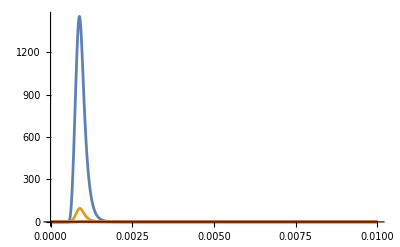

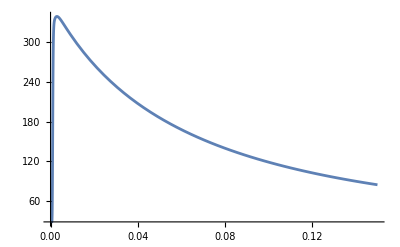

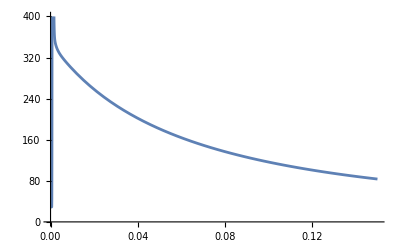

```mathematica
If[CaPlot==1,
Plot[
Evaluate[
Table[10^6/10^3*Ca[i][t], {i,{5, 25,100,200}}] /. sol], {t, 0., 0.01}, PlotRange -> All]] (*in µM*)

(*pl2a=If[AvCaPlot==1,
Plot[Evaluate[10^6*AvCa/.sol],{t,0,TimeWindow},PlotRange->All]]*)

pl2=If[AvCaPlot==1,
Plot[Evaluate[10^9/10^3*Caf/.sol],{t,0,TimeWindow},PlotRange->All]]  (*in nM*)

Plot[Evaluate[10^9/10^3*AvCa/.sol],{t,0,TimeWindow},PlotRange->{0.,400.}] (*in nM*)
```

## Data loading

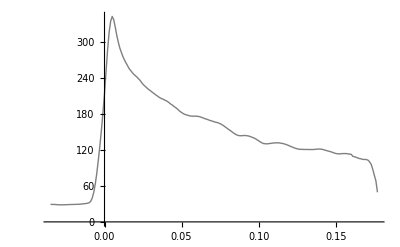

```mathematica
SetDirectory["/Users/hartmutschmidt/Documents/Cortical coupling distance map/Mathematica"];
(*DataAdult=Import["AgaConoSensitive.txt","Table"];*)
If[PFC==1,
DataPFC=Import["Ca_PFC.txt","Table"]];

If[adult==1,
sub=0.035];

(*ListPlot[DataPFC-sub]*)

pl1a=If[AvCaPlot==1,ListPlot[(DataPFC-sub),PlotRange->All,PlotStyle->{Gray, Thick},Joined->True]]
```

## Fitting

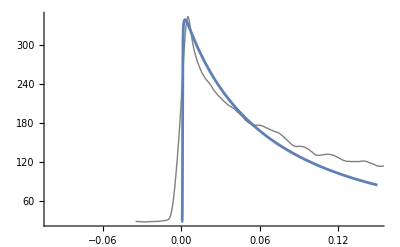

```mathematica
If[AvCaPlot==1,Show[pl1a,pl2,PlotRange->{{-0.1,0.15},All}]]  
(*in nM*)
```